```mathematica
Get[FileNameJoin[{NotebookDirectory[],"plot.m"}]]
```

```mathematica
BarChart[groupedData]
```

BarChart::ldata: <|{1.,1000.,1.}→{<|name→SGEMM/1000/1/1,iterations→85174,real_time→8229.36,cpu_time→8232.09,time_unit→ns,K→1.,M→1000.,N→1.,key→SMTAll|>,«1»,<|«1»|>,<|name→SGEMM/1000/1/1,iterations→86774,real_time→8059.92,«3»,M→1000.,N→1.,key→NoSMT8|>,<|name→SGEMM/1000/1/1,iterations→86109,real_time→8087.76,cpu_time→8090.34,time_unit→ns,K→1.,M→1000.,N→1.,key→NoSMT16|>},«88»,{«1»}→{«1»}|> is not a valid dataset or list of datasets.

BarChart[<|{1.,1000.,1.}→{<|name→SGEMM/1000/1/1,iterations→85174,real_time→8229.36,cpu_time→8232.09,time_unit→ns,K→1.,M→1000.,N→1.,key→SMTAll|>,<|name→SGEMM/1000/1/1,iterations→70553,5,N→1.,key→SMT16|>,<|1|>,<|1|>,<|name→SGEMM/1000/1/1,iterations→86109,real_time→8087.76,cpu_time→8090.34,time_unit→ns,K→1.,M→1000.,N→1.,key→NoSMT16|>},88,1|>]
 |  |  |  |

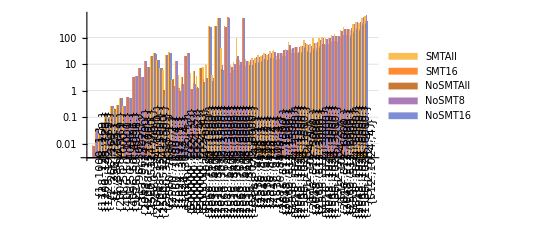

```mathematica
data=Take[groupedData,UpTo[100]];
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"cpu_time"]/10^6]],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```

```mathematica
1536*4608*1500
```

10616832000

```mathematica
2560*7680*1500
```

29491200000

```mathematica
Dataset[groupedData[{500000.0,512.0,1.0}]]
```

Dataset[<>]